```mathematica
<<"/Users/ethan/Desktop/WSS2017/saved_data/editInfo.mx"
<<"/Users/ethan/Desktop/WSS2017/saved_data/compData.mx"
```

```mathematica
urlForm = Flatten @ Table[StringReplace[i, " "-> "_"], {i, Keys[compData]}];
```

```mathematica
EditorStats[article_]:=
	If[
		Length@editInfo[article][[2]][[3]][[1]][[2;;]] ≤ 30,
		{Table[
			editInfo[article][[2]][[3]][[1]][[i]][[3]],
			{i, 2, Length@editInfo[article][[2]][[3]][[1]]}
		],
		Table[
			editInfo[article][[2]][[3]][[1]][[i]][[1]],
			{i, 2, Length@editInfo[article][[2]][[3]][[1]]}
		]},
		{Table[
			editInfo[article][[2]][[3]][[1]][[i]][[3]], {i, 2, 31}
		],
		Table[
			editInfo[article][[2]][[3]][[1]][[i]][[1]], {i, 2, 31}
		],
		editInfo[article][[2]][[3]][[1]][[32]]
		}
	]
editStats = AssociationMap[EditorStats,urlForm];
```

```mathematica
Block[{currentTotal},	
	TopEditorsText[article_] :=
		If[Length@editStats[article] == 2,
			currentTotal := 0;
			For[i = 1, i ≤ Length@editStats[article][[1]], i++,
				If[N@currentTotal / Total[editStats[article][[1]]] ≤ 0.5,
					currentTotal += editStats[article][[1]][[i]],
					Return[ToString[i - 1] <> " of " <> 
						ToString[Length@editStats[article][[1]]] <>
						" editors of made over 50% of "
						<> ToString[Total[editStats[article][[1]]]]
						<> " total edits on the article " <> article];
					Break[]
				]
			],
			currentTotal := 0;
			For[i = 1, i ≤ Length@editStats[article][[1]], i++,
				If[N@currentTotal / 
					(Total[editStats[article][[1]]] + editStats[article][[3]][[2]]) ≤ 0.5,
					currentTotal += editStats[article][[1]][[i]],
					Return[ToString[i - 1] <> " of " <>
						ToString[
							Length@editStats[article][[1]] + 
							ToExpression[StringTake[editStats[article][[3]][[1]],{1,-8}]]
						] <>
						" editors of made over 50% of " <> 
						ToString[Total[editStats[article][[1]]] + editStats[article][[3]][[2]]]
						<> " edits on the article " <> article];
					Break[]
				];
				If[i == Length@editStats[article][[1]],
						Return["The top 30 editors made " <> 
							ToString[100 * N@currentTotal / 
							(Total[editStats[article][[1]]] + editStats[article][[3]][[2]])]
							<> "% of " <> ToString[
							ToString[Total[editStats[article][[1]]] + 
							editStats[article][[3]][[2]]]]
							<> " edits on the article " <> article
						]
				]
			]
		]
]
```

```mathematica
(*Block[{currentTotal},	
	TopEditors[article_] :=
		If[Length@editStats[article] == 2,
			currentTotal := 0;
			For[i = 1, i ≤ Length@editStats[article][[1]], i++,
				If[N@currentTotal / Total[editStats[article][[1]]] ≤ 0.5,
					currentTotal += editStats[article][[1]][[i]],
					Return[
						N@((i - 1) / Length@editStats[article][[1]])
					];
					Break[]
				]
			],
			currentTotal := 0;
			For[i = 1, i ≤ Length@editStats[article][[1]], i++,
				If[N@currentTotal / 
					(Total[editStats[article][[1]]] + editStats[article][[3]][[2]]) ≤ 0.5,
					currentTotal += editStats[article][[1]][[i]],
					Return[
						N[(i - 1) / Length@editStats[article][[1]]]
					];
					Break[]
				];
				If[i == Length@editStats[article][[1]],
						Return["The top 30 editors made " <> 
							ToString[100 * N@currentTotal / 
							(Total[editStats[article][[1]]] + editStats[article][[3]][[2]])]
							<> "% of " <> ToString[
							ToString[Total[editStats[article][[1]]] + 
							editStats[article][[3]][[2]]]]
							<> " edits on the article " <> article
						]
				]
			]
		]
]*)
```

```mathematica
TopEditors[article_] :=
	If[Length@editStats[article] == 3,
		Return[
			N[
				100 * Total[editStats[article][[1]]] /
				(Total[editStats[article][[1]]] + editStats[article][[3]][[2]])
			]
		]
	]
```

```mathematica
Length@editStats["Computational_physics"][[1]]
```

30

```mathematica
thirtyPlus = DeleteCases[Table[If[Length@editStats[i] == 3 && editStats[i][[3]][[2]] > 0, i, ""],
	{i, urlForm}],""];
```

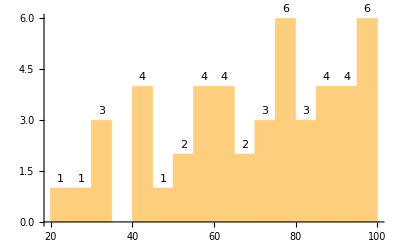

```mathematica
Histogram[AssociationMap[TopEditors,thirtyPlus],20,LabelingFunction->Above]
```